```mathematica
nodeNum=10;
weights = Parallelize[Table[RandomInteger[{1,40}], {i,nodeNum}]];
```

```mathematica
edgeNum =15;
g=RandomGraph[{nodeNum,edgeNum}];
While[!ConnectedGraphQ[g], g=RandomGraph[{nodeNum,edgeNum}];];
```

RandomGraph::args: RandomGraph[{nodeNum,15}] 使用无效参数调用.

General::stop: 在本次计算中，RandomGraph::args 的进一步输出将被抑制.

```mathematica
M={{0,0,0,0,1,1},{0,0,1,0,1,0},{1,0,0,1,0,0},
{0,0,0,0,1,0},{0,0,0,0,0,0},{0,0,0,1,0,0}};
weights = {65,99,62,35,38,39};
g=UndirectedGraph[AdjacencyGraph[M]];
edgeNum = Length[EdgeList[g]];
nodeNum=Length[weights];
```

```mathematica
g
```

-Graphics-

```mathematica
SetProperty[%121,VertexLabels->Table[i->x[[i]], {i,nodeNum}]]
```

-Graphics-

```mathematica
edges=Table[{i⟦1⟧,i⟦2⟧},{i,EdgeList[g]}];
A= SparseArray[{Join[Table[{i, edges[[i]][[1]]}, {i,Length[edges]}],Table[{i, edges[[i]][[2]]}, {i,Length[edges]}]]->Table[1, {i,Length[edges]*2}]},{edgeNum,nodeNum}];
```

```mathematica
x = LinearProgramming[weights, A,Table[1,{i, edgeNum}],Table[{0,1},{i, nodeNum}],Integers]
```

LinearProgramming::lpintrs: 当某些变量具有整数值时，方法 Simplex 对于 LinearProgramming 是无效的.

LinearProgramming[{65,99,62,35,38,39},SparseArray[…],{1,1,1,1,1,1,1,1},{{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}},ℤ,Method→Simplex]

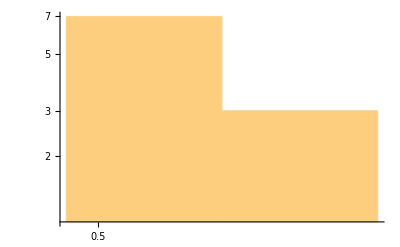

```mathematica
Histogram[x,"Log",ScalingFunctions->"Log"]
```

```mathematica
Total[Dot[weights,x]]
```

12650.1

```mathematica
a= ExampleData[{"LinearProgramming","osa-60"}];
```

```mathematica
b=Append[a, Method->"RevisedSimplex"];
```

```mathematica
AbsoluteTiming[x = LinearProgramming@@b;]
c = a[[1]];
```

{16.774,Null}

```mathematica
Dot[x,a[[1]]]
```

4.04407×10^6

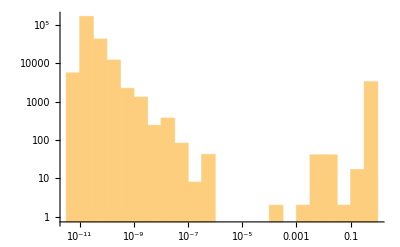

```mathematica
Histogram[x,"Log",ScalingFunctions->"Log"]
```

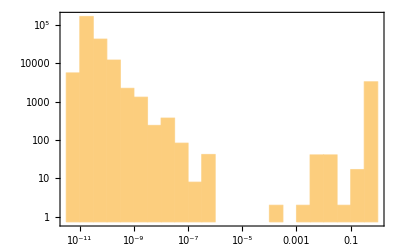

```mathematica
Histogram[x,"Log",PlotTheme->"Detailed",ScalingFunctions->"Log"]
```

```mathematica
b[[5]]
```

Method→InteriorPoint

```mathematica
MatrixPlot[%10]
```

MatrixPlot::mat0: 位置 1 处的变量 LinearProgramming[{2.82636, 16.3062, <<9997>>, 8.65995}, <<4>>] 不是一个矩阵.

MatrixPlot[LinearProgramming[1]]
 |  |  |  |

```mathematica
ExampleData[{"LinearProgramming","osa-60"}  ,"Source"]
```

http://www.netlib.org/lp/data/kennington/osa-60.gz

```mathematica
{"Collection","ConstraintMatrix","Dimensions","Equations","LinearProgrammingData","Name","Source"}
```

{Collection,ConstraintMatrix,Dimensions,Equations,LinearProgrammingData,Name,Source}

```mathematica
nodeNum=100000;
weights = Parallelize[Table[RandomReal[{1,40}], {i,nodeNum}]];
```

```mathematica
edgeNum =10000;
res = RandomInteger[{1,Max[Round[Divide[nodeNum, 3]], 1000]},edgeNum];
```

```mathematica
A = SparseArray[{Flatten[Table[Table[{i,RandomInteger[{1,nodeNum}]},{j,res[[i]]}],{i, edgeNum}],1]->Table[1,{k, Total[res]}]},{edgeNum,nodeNum}]
```

SparseArray[<15044315>, {1000, 100000}]

```mathematica
MatrixPlot[A,PlotTheme->"Detailed"]
```

-Graphics-

```mathematica
x=LinearProgramming[weights, A,Table[1,{i, edgeNum}],Table[{0,1},{i, nodeNum}]]
```

{8.54378×10^-14,3.60595×10^-14,1.00992×10^-13,5.69154×10^-14,4.35485×10^-14,2.23603×10^-14,99988,5.50897×10^-13,6.94153×10^-14,2.92211×10^-14,3.42015×10^-14,1.55964×10^-13,2.17794×10^-14}
 |  |  |  |

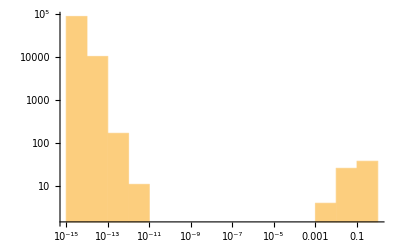

```mathematica
Histogram[x,"Log",ScalingFunctions->"Log"]
```

```mathematica
nodeNum=10000000;
weights=Parallelize[Table[RandomReal[{1,40}],{i,nodeNum}]];
edgeNum=5000;
res=RandomInteger[{1,Min[Round[Divide[nodeNum,3]],2000]},edgeNum];
```

```mathematica
A=SparseArray[{Flatten[Table[Table[{i,RandomInteger[{1,nodeNum}]},{j,res[[i]]}],{i,edgeNum}],1]->Table[1,{k,Total[res]}]},{edgeNum,nodeNum}]
```

SparseArray[<5027692>, {5000, 10000000}]